```mathematica
(* check yangians *)
```

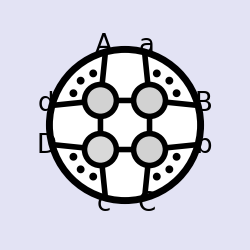
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
n=11;
<<"loop_amplitudes.m";
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>Sort[i] Signature[i]Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
cap2expand=ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h];
myBexp={ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]};
```

```mathematica
preyangcom[yang_,{a_,b_},{c_,d_,ee_}]:=Simplify[ab[n-1,n,2,3]/ab[n,1,2,3]((yang//todmatrix)/.DmatrixEval[{a,b},{c,n+1},{d,n+1},{ee,n+1}]//fullabB)//neab1]
yangcom[yang_,{a_,b_},{c_,d_,ee_}]:=Limit[e^2 neab1[Simplify[If[a>b,-yangcom[yang,{b,a},{c,d,ee}],
With[{hh=preyangcom[yang,{a,b},{c,d,ee}],c1=ab[n-1,n,2,3]/ab[n,1,2,3],c2=ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]},If[!IntersectingQ[{a,b},{1,2,n-1,n}],
hh,
Switch[{a,b},
{1,2},hh+c2 e^2 preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,2},{c,d,ee}],
{1,n-1},
hh-e preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,n-1},{c,d,ee}],
{1,n},
hh+preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,n},{c,d,ee}],
{1,_},
hh+c1 e τ preyangcom[yang,{n+1,b},{c,d,ee}],
{2,n-1},
hh-e preyangcom[yang,{2,n+1},{c,d,ee}]+c2 e^2  preyangcom[yang,{n+1,n-1},{c,d,ee}],
{2,n},
hh+preyangcom[yang,{2,n+1},{c,d,ee}]+c2 e^2  preyangcom[yang,{n+1,n},{c,d,ee}],
{2,_},
hh+c2 e^2 preyangcom[yang,{n+1,b},{c,d,ee}],
{_,n-1},
hh-e preyangcom[yang,{a,n+1},{c,d,ee}],
{n-1,n},
hh+ preyangcom[yang,{n-1,n+1},{c,d,ee}]-e preyangcom[yang,{n+1,n},{c,d,ee}],
{_,n},
hh+ preyangcom[yang,{a,n+1},{c,d,ee}],_,hh]]]]]],e->0]//Factor
qlogRcom[exp_,{a_,b_},{c_,d_,e_}]:=((exp/.qlogtodab//todoubleab//todmatrixn//fuse)/.dabne[{a,b}]/.DmatrixEval3[{c,d,e},3]/.cap2expand//neab1)/.dlog[x_]:>D[Log[x],τ]//Simplify//Factor
```

```mathematica
(* 1.1 *)
```

```mathematica
Union@Flatten@With[{a=2,b=4,c=5,d=6},
Simplify@Table[Union@Flatten[Table[yangcom[R[a,b,cap[{b,c},{d,n,n+1}],cap[{n,n+1},{b,c,d}],n+1]R[b,c,d,n,n+1],{i,j},{k,l,m}],{i,n},{j,i+1,n}]+Table[qlogRcom[-Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]dlog[ab[n,B,a,b]/ab[n,B,c,d]]R[a,b,c,d,n]/.ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y],{i,j},{k,l,m}]+qlogRcom[Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]dlog[ab[n,B,a,d]/ab[n,B,c,d]]R[a,b,c,d,n]/.ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y],{i,j},{k,l,m}],{i,n},{j,i+1,n}]],{k,n},{l,k+1,n},{m,l+1,n}]]
```

{0}

```mathematica
(* 1.2, 1.3, 1.4, 1.5 *)
```

```mathematica
Union@Flatten[Table[With[{a=2,b=4,c=5,d=6},
Simplify[yangcom[R[b,c,cap[{c,d},{n,n+1,a}],cap[{n+1,a},{c,d,n}],a]R[c,d,n,n+1,a],{i,j},{k,l,m}]-yangcom[R[a,b,c,d,n]R[a,cap[{c,d},{a,b,n}],d,n,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]]
```

```mathematica
Union@Flatten[Table[With[{a=2,b=4,c=5,d=6},
Simplify[yangcom[R[b,c,cap[{c,d},{n,n+1,a}],cap[{n+1,a},{c,d,n}],a]R[c,d,n,n+1,a],{i,j},{k,l,m}]-yangcom[R[a,b,c,d,n]R[a,cap[{a,b},{c,d,n}],d,n,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]]
```

```mathematica
Union@Flatten[Table[With[{a=2,b=4,c=5,d=6},
Simplify[yangcom[R[d,n,cap[{n,n+1},{a,b,c}],cap[{b,c},{n,n+1,a}],c]R[a,b,c,n,n+1],{i,j},{k,l,m}]-yangcom[R[b,c,d,n,n+1]R[a,b,cap[{b,c},{d,n,n+1}],cap[{n,n+1},{b,c,d}],n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]]
```

```mathematica
Union@Flatten[Table[With[{a=2,b=4,c=5,d=6},
Simplify[yangcom[R[n,n+1,cap[{n+1,a},{b,c,d}],cap[{c,d},{n+1,a,b}],d]R[a,b,c,d,n+1],{i,j},{k,l,m}]-yangcom[R[a,b,c,d,n]R[cap[{n,a},{b,c,d}],cap[{c,d},{n,a,b}],d,n,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]]
```

```mathematica
(* 1.6 *)
```

```mathematica
(* 2.1 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=2,b=4,c=6,d=8,ee=9},Simplify[
qlogRcom[#,{i,j},{k,l,m}]&/@((Qlog[ab[1,cap[{a,b},{c,d,ee}],n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,d,ee]dlog[ab[n,B,ee,cap[{a,b},{c,d,ee}]]/ab[n,B,a,b]]+
Qlog[ab[1,a,n-1,n]/ab[1,ee,n-1,n]]R[a,c,d,ee,n]dlog[ab[n,B,a,ee]/ab[n,B,a,b]]-
Qlog[ab[1,b,n-1,n]/ab[1,ee,n-1,n]]R[b,c,d,ee,n]dlog[ab[n,B,b,ee]/ab[n,B,a,b]]+
Qlog[ab[1,cap[{a,b},{c,ee,n}],n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,ee,n]dlog[ab[n,B,c,ee]/ab[n,B,a,b]]-
Qlog[ab[1,cap[{a,b},{d,ee,n}],n-1,n]/ab[1,ee,n-1,n]]R[a,b,d,ee,n]dlog[ab[n,B,d,ee]/ab[n,B,a,b]]-
Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,d,n]dlog[ab[n,B,ee,cap[{a,b},{c,d,n}]]/ab[n,B,a,b]])/.ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y])]+yangcom[R[a,b,cap[{c,d},{ee,n,n+1}],cap[{n,n+1},{c,d,ee}],n+1]R[c,d,ee,n,n+1],{i,j},{k,l,m}]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]
```

{0}

```mathematica
(* 2.2 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=2,b=4,c=6,d=8,ee=9},
qlogRcom[dlog[τ/ab[n,B,a,b]]
Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[a, b, cap[{c,d},{n-1,n,1}], n-1, n]/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]},{i,j},{k,l,m}]+yangcom[R[a,b,cap[{c,d},{n-1,n,n+1}],cap[{n,n+1},{c,d,n-1}],n+1] R[c,d,n-1,n,n+1],{i,j},{k,l,m}]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]
```

```mathematica
(* 2.3 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=2,b=4,c=6,d=8,ee=9},Simplify[
qlogRcom[#,{i,j},{k,l,m}]&/@(Expand[Qlog[ab[1,b,n-1,n]/ab[1,ee,n-1,n]](
R[1,b,c,d,ee]dlog[ab[n,B,ee,cap[{1,b},{c,d,ee}]]]-
R[1,b,c,d,n]dlog[ab[n,B,ee,cap[{1,b},{c,d,n}]]]-
R[b,c,d,ee,n]dlog[ab[n,B,b,ee]]+
R[1,b,c,ee,n]dlog[ab[n,B,c,ee]]-
R[1,b,d,ee,n]dlog[ab[n,B,d,ee]]
)]/.ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y])]+yangcom[R[1,b,cap[{c,d},{ee,n,n+1}],cap[{n,n+1},{c,d,ee}],n+1] R[c,d,ee,n,n+1],{i,j},{k,l,m}]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]
```

{0}

```mathematica
(* 2.4 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=3,b=4,c=6,d=8,ee=9},
yangcom[R[1,b,cap[{c,d},{n-1,n,n+1}],cap[{n,n+1},{c,d,n-1}],n+1] R[c,d,n-1,n,n+1],{i,j},{k,l,m}]+qlogRcom[Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]]R[1,c,d,n-1,n]dlog[τ],{i,j},{k,l,m}]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

```mathematica
(* 2.5 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=2,b=4,c=6,d=8,ee=9},yangcom[#,{i,j},{k,l,m}]&/@Expand[R[b, c,cap[{d, ee},{n, n+1, a}],cap[{n+1, a},{d, ee, n}], a] R[a, d, ee, n, n+1]-(R[a,b,c,d,n] R[a,d,ee,n,n+1]+R[a,cap[{d,ee},{b,c,n}],ee,n,n+1] R[b,c,d,ee,n]-R[a,cap[{d, ee},{a, b, c}], ee,  n, n+1] R[a, b, c, d, ee]+R[a,cap[{d, ee},{a,b,n}], ee, n, n+1] R[a, b, d, ee, n]-R[a,cap[{d, ee},{a, c, n}], ee, n, n+1] R[a, c, d, ee, n])]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{397.127,{0}}

```mathematica
(* 2.6 *)
```

```mathematica
Union@Flatten@Table[Simplify@With[{a=2,b=4,c=6,d=8,ee=9},
yangcom[R[c,d,cap[{ee,n},{n+1,a,b}],cap[{a,b},{ee,n,n+1}],b]R[a,b,ee,n,n+1],{i,j},{k,l,m}]-yangcom[R[a,cap[{a,b},{c,d,n}],ee,n,n+1]R[a,b,c,d,n],{i,j},{k,l,m}]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]
```

{0}

```mathematica
(* 2.7 *)
```

```mathematica
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,ee,cap[{n,n+1},{a,b,c}],cap[{b,c},{n,n+1,a}],c]R[a,b,c,n,n+1],{i,j},{k,l,m}]+qlogRcom[Expand[R[a,b,c,d,ee](Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],a]/ab[n,B,a,b]]+Qlog[ab[1,cap[{d,ee},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,ee}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],c]/ab[n,B,a,b]])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{142.79,{0}}

```mathematica
(* 2.8 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,ee,cap[{n,n+1},{a,b,c}],cap[{b,c},{n,n+1,a}],c]R[a,b,c,n,n+1],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],a]/ab[n,B,a,b]]R[a,b,c,d,ee]+Qlog[ab[1,cap[{d,ee},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,ee}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],c]/ab[n,B,a,b]]R[a,b,c,d,ee])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{151.319,{0}}

```mathematica
(* 2.9 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,ee,cap[{n,n+1},{1,b,c}],cap[{b,c},{n,n+1,1}],c] R[1,b,c,n,n+1],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,cap[{b,c},{d,ee,1}],n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,cap[{d,ee},{1,b,c}],c]]R[1,b,c,d,ee])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{127.519,{0}}

```mathematica
(* 2.10 *)
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,n-1,cap[{n,n+1},{a,b,c}],cap[{b,c},{n,n+1,a}],c] R[a,b,c,n,n+1],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]dlog[ab[n,B,cap[{d,n-1},{a,b,c}],a]/ab[n,B,a,b]]R[a,b,c,d,n-1]+Qlog[ab[1,d,n-1,n]/ab[1,cap[{a,b},{c,d,n-1}],n-1,n]]dlog[ab[n,B,cap[{d,n-1},{a,b,c}],c]/ab[n,B,a,b]]R[a,b,c,d,n-1])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{108.116,{0}}

```mathematica
(* 2.11 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,n-1,cap[{n,n+1},{1,b,c}],cap[{b,c},{n,n+1,1}],c] R[1,b,c,n,n+1],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,d,n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,cap[{d,n-1},{1,b,c}],c]]R[1,b,c,d,n-1])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{94.2481,{0}}

```mathematica
(* 2.12 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[ee,n,cap[{n+1,a},{b,c,d}],cap[{c,d},{n+1,a,b}],d] R[a,b,c,d,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{83.0858,{0}}

```mathematica
(* 2.13, 2.14 *)
```

```mathematica
(* 2.15 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[n+1,a,cap[{b,c},{d,n-1,n}],cap[{n-1,n},{b,c,d}],n] R[b,c,d,n-1,n],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]dlog[τ/ab[n,B,a,cap[{b,c},{d,n-1,n}]]]R[b,c,d,n-1,n])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{97.0916,{0}}

```mathematica
(* 2.16 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[n+1,1,cap[{b,c},{d,n-1,n}],cap[{n-1,n},{b,c,d}],n] R[b,c,d,n-1,n],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,2,n-1,n]/ab[1,d,n-1,n]]dlog[τ]R[b,c,d,n-1,n])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{86.9406,{0}}

```mathematica
(* 3.1 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=8,ee=9},
yangcom[R[a,b,c,cap[{n,n+1},{c,d,ee}],n+1]R[c,d,ee,n,n+1],{i,j},{k,l,m}]+qlogRcom[(-Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],c,d,ee,n]dlog[ab[n,B,a,b]]+
Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,c},{d,ee,n}],n-1,n]]R[a,c,d,ee,n]dlog[ab[n,B,a,c]]-
Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,ee,n}],n-1,n]]R[b,c,d,ee,n]dlog[ab[n,B,b,c]]+
Qlog[ab[1,cap[{a,b},{c,d,ee}],n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]R[a,b,c,d,ee]dlog[ab[n,B,cap[{a,b},{c,d,ee}],c]]+
Qlog[ab[1,d,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]R[a,b,c,d,n]dlog[ab[n,B,c,d]]+
Qlog[ab[1,cap[{a,b},{c,ee,n}],n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,ee,n]dlog[ab[n,B,c,ee]]-
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]])/.myBexp,{i,j},{k,l,m}]
],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{102.779,{0}}

```mathematica
(* 3.2 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=8,ee=9},yangcom[R[1,b,c,cap[{n,n+1},{c,d,ee}],n+1] R[c,d,ee,n,n+1],{i,j},{k,l,m}]+
qlogRcom[
(
-Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,ee,n}],n-1,n]]R[b,c,d,ee,n]dlog[ab[n,B,b,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,cap[{d,ee},{1,b,c}],n-1,n]]R[1,b,c,d,ee]dlog[ab[n,B,cap[{1,b},{c,d,ee}],c]]-
Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]]dlog[ab[n,B,c,d]]R[1,b,c,d,n]+
Qlog[ab[1,b,n-1,n]/ab[1,ee,n-1,n]]dlog[ab[n,B,c,ee]]R[1,b,c,ee,n]-
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]dlog[ab[n,B,d,ee]]R[1,b,c,cap[{d,ee},{n-1,n,1}],n]
)/.myBexp,{i,j},{k,l,m}]
],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{210.041,{0}}

```mathematica
(* 3.3 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=8,ee=9},yangcom[R[a,b,c,cap[{n,n+1},{c,d,n-1}],n+1]R[c,d,n-1,n,n+1],{i,j},{k,l,m}]+
qlogRcom[
(
Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]]R[a,b,c,n-1,n]dlog[τ]-
Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],c,d,n-1,n]dlog[ab[n,B,a,b]]+
Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]R[a,c,d,n-1,n]dlog[ab[n,B,a,c]]-
Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]]R[b,c,d,n-1,n]dlog[ab[n,B,b,c]]-
Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,d,n-1,n]]R[a,b,c,d,n]dlog[ab[n,B,c,d]]+
Qlog[ab[1,cap[{a,b},{c,d,n-1}],n-1,n]/ab[1,d,n-1,n]]R[a,b,c,d,n-1]dlog[ab[n,B,cap[{a,b},{c,d,n-1}],c]]
)/.myBexp,{i,j},{k,l,m}]
],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{90.4937,{0}}

```mathematica
(* 3.4 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=8,ee=9},yangcom[R[1,b,c,cap[{n,n+1},{c,d,n-1}],n+1]R[c,d,n-1,n,n+1],{i,j},{k,l,m}]+
qlogRcom[
Expand[Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]](
-R[b,c,d,n-1,n]dlog[ab[n,B,b,c]]-
R[1,b,c,d,n]dlog[ab[n,B,c,d]]+
R[1,b,c,n-1,n]dlog[τ]+
R[1,b,c,d,n-1]dlog[ab[n,B,cap[{1,b},{c,d,n-1}],c]]
)/.myBexp],{i,j},{k,l,m}]
],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{60.2497,{0}}

```mathematica
(* 3.5 *)
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[b,c,d,cap[{n+1,a},{d,ee,n}],a] R[d,ee,n,n+1,a],{i,j},{k,l,m}]-yangcom[R[b,c,d,n,a] R[a,d,ee,n,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{114.793,{0}}

```mathematica
(* 3.6 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=8,ee=9},yangcom[R[c,d,ee,cap[{a,b},{ee,n,n+1}],b]R[ee,n,n+1,a,b],{i,j},{k,l,m}]+
qlogRcom[
Expand[R[a,b,c,d,ee](
Qlog[ab[1,cap[{a,b},{c,d,ee}],n-1,n]/ab[1,a,n-1,n]]dlog[ab[n,B,a,b]/ab[n,B,cap[{a,b},{c,d,ee}],ee]]+
Qlog[ab[1,a,n-1,n]/ab[1,ee,n-1,n]]dlog[ab[n,B,a,ee]/ab[n,B,cap[{a,b},{c,d,ee}],ee]]
)/.myBexp],{i,j},{k,l,m}]
],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{141.094,{0}}

```mathematica
(* 3.7 *)
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[c,d,n-1,cap[{a,b},{n-1,n,n+1}],b] R[n-1,n,n+1,a,b],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n-1}],n-1,n]]dlog[τ/ab[n,B,a,b]]R[a,b,c,d,n-1])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{74.2839,{0}}

```mathematica
(* 3.8 *)
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[c,d,ee,cap[{1,b},{ee,n,n+1}],b] R[ee,n,n+1,1,b],{i,j},{k,l,m}]+qlogRcom[((Qlog[ab[1,ee,n-1,n]/ab[1,b,n-1,n]]dlog[ab[ee,n,B,cap[{1,b},{ee,c,d}]]]R[1,b,c,d,ee])/.{ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3]ab[x,1,y]}),{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{116.1,{0}}

```mathematica
(* 3.9 *)
Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[c,d,n-1,cap[{1,b},{n-1,n,n+1}],b] R[n-1,n,n+1,1,b],{i,j},{k,l,m}]+qlogRcom[(Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]]dlog[τ]R[1,b,c,d,n-1])/.myBexp,{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{63.5137,{0}}

```mathematica
(* 3.10 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,ee,n,cap[{b,c},{n,n+1,a}],c]R[n,n+1,a,b,c],{i,j},{k,l,m}]+qlogRcom[Expand[R[b,c,d,ee,n](Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]dlog[ab[n,B,a,b]/ab[n,B,a,cap[{b,c},{d,ee,n}]]]+
Qlog[ab[1,cap[{b,c},{d,ee,n}],n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,b,c]/ab[n,B,a,cap[{b,c},{d,ee,n}]]]
)/.myBexp],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{95.0282,{0}}

```mathematica
(* 3.11 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,n-1,n,cap[{b,c},{n,n+1,a}],c]R[n,n+1,a,b,c],{i,j},{k,l,m}]+qlogRcom[Expand[R[b,c,d,n-1,n](Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]dlog[ab[n,B,a,b]/ab[n,B,a,cap[{b,c},{d,n-1,n}]]]+
Qlog[ab[1,d,n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,b,c]/ab[n,B,a,cap[{b,c},{d,n-1,n}]]]
)/.myBexp],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{91.6206,{0}}

```mathematica
(* 3.12 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,ee,n,cap[{b,c},{n,n+1,1}],c]R[n,n+1,1,b,c],{i,j},{k,l,m}]+qlogRcom[R[b,c,d,ee,n]Qlog[ab[1,cap[{b,c},{d,ee,n}],n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,b,c]]/.myBexp,{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{61.3979,{0}}

```mathematica
(* 3.13 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[d,n-1,n,cap[{b,c},{n,n+1,1}],c]R[n,n+1,1,b,c],{i,j},{k,l,m}]+qlogRcom[R[b,c,d,n-1,n]Qlog[ab[1,d,n-1,n]/ab[1,b,n-1,n]]dlog[ab[n,B,b,c]]/.myBexp,{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{64.856,{0}}

```mathematica
(* 3.14 *)

Union@Flatten@Table[With[{a=2,b=4,c=6,d=8,ee=9},Simplify[yangcom[R[ee,n,n+1,cap[{c,d},{n+1 ,a ,b}],d] R[n+1,a,b,c,d],{i,j},{k,l,m}]-
yangcom[R[a,b,c,d,n]R[cap[{c,d},{n,a,b}],d,ee,n,n+1],{i,j},{k,l,m}]]],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{130.06,{0}}

```mathematica
(* 3.15, 3.16 *)
```

```mathematica
(* 4.1 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[a,b,c,cap[{n,n+1},{d,ee,f}],n+1]R[d,ee,f,n,n+1],{i,j},{k,l,m}]+qlogRcom[(
Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,b]]-
Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]R[cap[{a,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,b,c]]+
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,ee]]-
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,f]]+
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,ee,f]]
)/.myBexp
,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

$Aborted

```mathematica
(* 4.2 *)

Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[1,b,c,cap[{n,n+1},{d,ee,f}],n+1]R[d,ee,f,n,n+1],{i,j},{k,l,m}]+
qlogRcom[(
-Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,b,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[1,cap[{b,c},{n-1,n,1}],d,ee,f]dlog[ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,d,f]]-
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,ee,f]]
)/.myBexp
,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{142.386,{0}}

```mathematica
(* 4.3 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[a,b,c,cap[{n,n+1},{d,ee,n-1}],n+1]R[d,ee,n-1,n,n+1],{i,j},{k,l,m}]+qlogRcom[Expand[
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[a,b,c,n-1,n]dlog[τ/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,b]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]+
R[a,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{295.009,{0}}

```mathematica
(* 4.4 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[1,b,c,cap[{n,n+1},{d,ee,n-1}],n+1]R[d,ee,n-1,n,n+1],{i,j},{k,l,m}]+qlogRcom[Expand[
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[1,b,c,n-1,n]dlog[τ]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]]-
R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
R[1,b,c,cap[{d,ee},{n-1,n,1}],n-1]dlog[ab[n,B,cap2[{1,b,c},{d,ee,n-1}]]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{125.428,{0}}

```mathematica
(* 4.5 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[b,c,d,cap[{n+1,a},{d,ee,n}],a] R[d,ee,n,n+1,a] ,{i,j},{k,l,m}]-yangcom[R[b,c,d,n,a] R[a,d,ee,n,n+1],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{214.898,{0}}

```mathematica
(* 4.6  *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[c,d,ee,cap[{a,b},{f,n,n+1}],b] R[a,b,f,n,n+1] ,{i,j},{k,l,m}]-yangcom[R[a,cap[{a,b},{c,d,ee}],f,n,n+1] R[a,b,c,d,ee] ,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{171.705,{0}}

```mathematica
(* 4.7 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[d,ee,f,cap[{b,c},{n,n+1,a}],c] R[n,n+1,a,b,c] ,{i,j},{k,l,m}]-yangcom[R[a,b,cap[{b,c},{d,ee,f}],n,n+1] R[b,c,d,ee,f] ,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{151.454,{0}}

```mathematica
(* 4.8 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[ee,f,n,cap[{c,d},{n+1,a,b}],d] R[n+1,a,b,c,d] ,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{79.2235,{0}}

```mathematica
(* 4.9, 4.10, 4.11 *)
```

```mathematica
(* 5 *)
```

```mathematica
(* 6.1 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[a,b,c,cap[{d,ee},{f,n,n+1}],n+1]R[d,ee,f,n,n+1],{i,j},{k,l,m}]+qlogRcom[Expand[
(
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,d,n]dlog[ab[n,B,d,f]/ab[n,B,d,ee]]-
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,ee,n]dlog[ab[n,B,ee,f]/ab[n,B,d,ee]]-
Qlog[ab[1,cap[{d,ee},{a,b,c}],n-1,n]/ab[1,f,n-1,n]]R[a,b,c,d,ee]dlog[ab[n,B,cap[{d,ee},{a,b,c}],f]/ab[n,B,d,ee]]+
Qlog[ab[1,cap[{a,b},{d,ee,n}],n-1,n]/ab[1,f,n-1,n]]R[a,b,d,ee,n]dlog[ab[n,B,cap[{a,b},{d,ee,n}],f]/ab[n,B,d,ee]]-
Qlog[ab[1,cap[{a,c},{d,ee,n}],n-1,n]/ab[1,f,n-1,n]]R[a,c,d,ee,n]dlog[ab[n,B,cap[{a,c},{d,ee,n}],f]/ab[n,B,d,ee]]+
Qlog[ab[1,cap[{b,c},{d,ee,n}],n-1,n]/ab[1,f,n-1,n]]R[b,c,d,ee,n]dlog[ab[n,B,cap[{b,c},{d,ee,n}],f]/ab[n,B,d,ee]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{355.805,{0}}

```mathematica
(* 6.2 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[a,b,c,cap[{d,ee},{n-1,n,n+1}],n+1]R[d,ee,n-1,n,n+1],{i,j},{k,l,m}]+qlogRcom[Expand[
(
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[τ/ab[n,B,d,ee]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{223.204,{0}}

```mathematica
(* 6.3 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[b,c,d,cap[{ee,f},{n,n+1,a}],a]R[ee,f,n,n+1,a],{i,j},{k,l,m}]+qlogRcom[Expand[
(
-Qlog[ab[1,a,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,d,ee]dlog[ab[n,B,a,ee]/ab[n,B,ee,f]]+
Qlog[ab[1,a,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,d,f]dlog[ab[n,B,a,f]/ab[n,B,ee,f]]+
Qlog[ab[1,cap[{ee,f},{a,b,c}],n-1,n]/ab[1,a,n-1,n]]R[a,b,c,ee,f]dlog[ab[n,B,cap[{ee,f},{a,b,c}],a]/ab[n,B,ee,f]]-
Qlog[ab[1,cap[{ee,f},{a,b,d}],n-1,n]/ab[1,a,n-1,n]]R[a,b,d,ee,f]dlog[ab[n,B,cap[{ee,f},{a,b,d}],a]/ab[n,B,ee,f]]+
Qlog[ab[1,cap[{ee,f},{a,c,d}],n-1,n]/ab[1,a,n-1,n]]R[a,c,d,ee,f]dlog[ab[n,B,cap[{ee,f},{a,c,d}],a]/ab[n,B,ee,f]]-
Qlog[ab[1,cap[{ee,f},{b,c,d}],n-1,n]/ab[1,a,n-1,n]]R[b,c,d,ee,f]dlog[ab[n,B,cap[{ee,f},{b,c,d}],a]/ab[n,B,ee,f]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{249.715,{0}}

```mathematica
(* 6.4 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[b,c,d,cap[{ee,n-1},{n,n+1,a}],a]R[ee,n-1,n,n+1,a],{i,j},{k,l,m}]+qlogRcom[Expand[
Qlog[ab[1,a,n-1,n]/ab[1,ee,n-1,n]](
R[a,b,c,d,n-1]dlog[τ/ab[n,B,cap[{ee,n-1},{b,c,d}],a]]-
R[a,b,c,d,ee]dlog[ab[n,B,a,ee]/ab[n,B,cap[{ee,n-1},{b,c,d}],a]]-
R[a,b,c,ee,n-1]dlog[ab[n,B,cap[{ee,n-1},{a,b,c}],a]/ab[n,B,cap[{ee,n-1},{b,c,d}],a]]+
R[a,b,d,ee,n-1]dlog[ab[n,B,cap[{ee,n-1},{a,b,d}],a]/ab[n,B,cap[{ee,n-1},{b,c,d}],a]]-
R[a,c,d,ee,n-1]dlog[ab[n,B,cap[{ee,n-1},{a,c,d}],a]/ab[n,B,cap[{ee,n-1},{b,c,d}],a]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{209.755,{0}}

```mathematica
(* 6.5 *)

Union@Flatten@Table[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[b,c,d,cap[{ee,f},{n,n+1,1}],1]R[ee,f,n,n+1,1],{i,j},{k,l,m}]+qlogRcom[-(R[1,b,c,d,cap[{ee,f},{n-1,n,1}]]dlog[ab[n,B,ee,f]]Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]])/.myBexp,{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{125.417,{0}}

```mathematica
(* 6.6 *)

Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[b,c,d,cap[{ee,n-1},{n,n+1,1}],1]R[ee,n-1,n,n+1,1],{i,j},{k,l,m}]+qlogRcom[R[1,b,c,d,n-1]dlog[τ]Qlog[ab[1,2,n-1,n]/ab[1,ee,n-1,n]],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{65.5504,{0}}

```mathematica
(* 6.7 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[c,d,ee,cap[{f,n},{n+1,a,b}],b]R[f,n,n+1,a,b],{i,j},{k,l,m}]-yangcom[R[b,c,d,ee,n]R[a,b,f,n,n+1],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{80.7975,{0}}

```mathematica
(* 6.8 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[d,ee,f,cap[{n,n+1},{a,b,c}],c]R[n,n+1,a,b,c],{i,j},{k,l,m}]+qlogRcom[Expand[
(
-Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],c,d,ee,f]dlog[ab[n,B,a,b]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]+
Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,c},{d,ee,f}],n-1,n]]R[a,c,d,ee,f]dlog[ab[n,B,a,c]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]-
Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,ee,f}],n-1,n]]R[b,c,d,ee,f]dlog[ab[n,B,b,c]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]+
Qlog[ab[1,cap[{a,b},{c,d,ee}],n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]R[a,b,c,d,ee]dlog[ab[n,B,cap[{a,b},{c,d,ee}],c]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]-
Qlog[ab[1,cap[{a,b},{c,d,f}],n-1,n]/ab[1,cap[{d,f},{a,b,c}],n-1,n]]R[a,b,c,d,f]dlog[ab[n,B,cap[{a,b},{c,d,f}],c]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]+
Qlog[ab[1,cap[{a,b},{c,ee,f}],n-1,n]/ab[1,cap[{ee,f},{a,b,c}],n-1,n]]R[a,b,c,ee,f]dlog[ab[n,B,cap[{a,b},{c,ee,f}],c]/ab[n,B,cap2[{a,b,c},{d,ee,f}]]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{229.846,{0}}

```mathematica
(* 6.9 *)
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[d,ee,f,cap[{n,n+1},{1,b,c}],c]R[n,n+1,1,b,c],{i,j},{k,l,m}]+qlogRcom[Expand[
(
-Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,ee,f}],n-1,n]]R[b,c,d,ee,f]dlog[ab[n,B,b,c]/ab[n,B,cap2[{1,b,c},{d,ee,f}]]]+
Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,ee,1}],n-1,n]]R[1,b,c,d,ee]dlog[ab[n,B,cap[{1,b},{c,d,ee}],c]/ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-
Qlog[ab[1,b,n-1,n]/ab[1,cap[{d,f},{1,b,c}],n-1,n]]R[1,b,c,d,f]dlog[ab[n,B,cap[{1,b},{c,d,f}],c]/ab[n,B,cap2[{1,b,c},{d,ee,f}]]]+
Qlog[ab[1,b,n-1,n]/ab[1,cap[{ee,f},{1,b,c}],n-1,n]]R[1,b,c,ee,f]dlog[ab[n,B,cap[{1,b},{c,ee,f}],c]/ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[1,c,d,ee,f]dlog[ab[n,B,cap2[{1,b,c},{d,ee,f}]]]
)/.myBexp
],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{148.896,{0}}

```mathematica
(* 6.10 *)
```

```mathematica
Union@Flatten@ParallelTable[Simplify@Block[{a=2,b=4,c=6,d=7,ee=8,f=9},yangcom[R[ee,f,n,cap[{n+1,a},{b,c,d}],d]R[n+1,a,b,c,d],{i,j},{k,l,m}]],
{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming
```

{76.4627,{0}}

```mathematica
(* 6.11, 6.12, 6.13 *)
```

```mathematica
myocr[string_]:=StringReplace[StringReplace[StringReplace[string,{"i_{1}"->"a","i_{2}"->"b","i_{3}"->"c","i_{4}"->"d","i_{5}"->"ee","\\left"|"\\right"->""}],{
"("~~Shortest[x__]~~") \\cap("~~Shortest[y__]~~")":>"cap[{"~~x~~"},{"~~y~~"}]",
"\\langle"~~Shortest[x__]~~"\\rangle":>"ab["~~x~~"]"
}],{"\\bar{n} "~~x_:>"1,"~~x~~",n-1,n","\\frac{"~~Shortest[x__]~~"}{":>x~~"/"}]
```

```mathematica
myocr["R\\left[i_{5}, n, n+1,\\left(n+1 i_{1} i_{2}\\right) \\cap\\left(i_{3} i_{4}\\right), i_{4}\\right] R\\left[n+1, i_{1}, i_{2}, i_{3}, i_{4}\\right]"]
```

R[ee, n, n+1,cap[{n+1 a b},{c d}], d] R[n+1, a, b, c, d]